```mathematica
Quit
```

## MC Values (from Jess)

```mathematica
SetDirectory["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Mathematica codes/MC Results"];
```

```mathematica
mcmcFiles=<|"Model 1"->"mcmc_parameter_summary_model_1_20000steps.csv","Model 2"->"mcmc_parameter_summary_model_2_20000steps.csv","Model 3"->"mcmc_parameter_summary_model_3_50000steps.csv"|>;
```

```mathematica
paramColumnMap=<|"H0_mean"->"H0","q0_mean"->"q0","j0_mean"->"j0","Om0_mean"->"Om0","eps_mean"->"eps","wDE0_mean"->"wDE0","wDE0p_mean"->"wDE0p"|>;
```

```mathematica
(*Build the nested association for a single model's CSV file*)
BuildModelParams[file_String]:=Module[{data,header,rows},data=Import[file,"Data"];
header=First[data];
rows=Rest[data];
Association[Map[Function[row,Module[{assocFull,datasetName},assocFull=AssociationThread[header->row];
datasetName=assocFull["dataset"];
datasetName->Association[KeyValueMap[Function[{oldKey,newKey},newKey->assocFull[oldKey]],paramColumnMap]]]],rows]]];
```

```mathematica
(*Master nested association:allParams["Model 1"]["DESI"]-><|"H0"->...,...|>*)
allParams=Association[KeyValueMap[Function[{modelName,file},modelName->BuildModelParams[file]],mcmcFiles]];
```

```mathematica
(* ============================================================*)
(*Convenience accessors*)
(* ============================================================*)

(*List available models*)
AvailableModels[]=Keys[allParams];
AvailableDatasets[model_String]:=Keys[allParams[model]];
```

```mathematica
AvailableModels[]
```

{Model 1,Model 2,Model 3}

```mathematica
AvailableDatasets["Model 1"]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
(*(*Main getter:GetParams["Model 1","DESI"]->Association of params*)
GetParams[model_String,dataset_String]:=Module[{},If[!KeyExistsQ[allParams,model],Message[GetParams::nomodel,model,AvailableModels[]];
Return[$Failed]];
If[!KeyExistsQ[allParams[model],dataset],Message[GetParams::nodataset,dataset,model,AvailableDatasets[model]];
Return[$Failed]];
allParams[model][dataset]];

GetParams::nomodel="Model `1` not found. Available models: `2`";
GetParams::nodataset="Dataset `1` not found for `2`. Available datasets: `3`";*)
```

```mathematica
(*Map model name->jModel function*)
jModelMap=<|"Model 1"->j1,"Model 2"->j2,"Model 3"->j3|>;
```

```mathematica
(*Main getter:GetParams["Model 1","DESI"]->Association of params,including "j"*)
GetParams[model_String,dataset_String]:=Module[{baseParams},If[!KeyExistsQ[allParams,model],Message[GetParams::nomodel,model,AvailableModels[]];
Return[$Failed]];
If[!KeyExistsQ[allParams[model],dataset],Message[GetParams::nodataset,dataset,model,AvailableDatasets[model]];
Return[$Failed]];
baseParams=allParams[model][dataset];
Append[baseParams,"j"->jModelMap[model]]];
```

### Model 1:

#### Desi Values

```mathematica
params1a=GetParams["Model 1","DESI"];
params1a["q0"]
params1a["Om0"]
params1a["eps"]
params1a["H0"]
```

-0.517033

0.498537

-0.0258394

68.2919

```mathematica
(*H01a=68.29192059313633;
q01a=-0.5170327771473278;
j01a=0.9625363652579005;
Ωm01a=0.4985365526609583;
ϵ1a=-0.025839351696166715;
wDE01a=-1.3514167286778105;*)
```

```mathematica
params10a=GetParams["Model 1","Planck + Union3 + Pantheon+ + DESY5"];
params10a["q0"]
params10a["Om0"]
params10a["eps"]
params10a["H0"]
```

-0.516172

0.31252

0.00132349

67.7409

### Model 2:

#### Desi Values

```mathematica
params2a=GetParams["Model 2","DESI"];
params2a["q0"]
params2a["Om0"]
params2a["eps"]
params2a["H0"]
```

-0.49883

0.491401

-0.100239

68.5342

```mathematica
H02a=68.53416748702578;
q02a=-0.49882983918505364;
j02a=0.8997606059127958;
Ωm02a=0.4914005086938241;
ϵ2a=-0.025839351696166715;
wDE02a=-1.3078293508597978;
```

### Model 3:

#### Desi Values

```mathematica
H03a=68.05462677945144;
q03a=-0.48266330038260274;
j03a=0.8033876955633561;
Ωm03a=0.5039105165387399;
ϵ3a=0.06671817784473298;
wDE03a=-1.3283914786225075;
```

## Equations

```mathematica
zPlot=10;
zinitial=100;
```

#### Defining the system of equations

```mathematica
dx= (1+z)x'[z]-(x[z]^2-x[z](2+q[z])-2-2q[z]+3Ω[z])==0;
dΩ=(1+z)Ω'[z]-Ω[z](x[z]+1-2q[z])==0;
dq=(1+z)q'[z]- (j[z]-q[z]-2 q[z]^2)==0;
dj= (1+z)j'[z]- (-s[z]-j[z](2+3q[z]))==0;
ds=(1+z)s'[z]- (-l[z]-s[z](3+4q[z]))==0;
dEh=(1+z)Eh'[z]- Eh[z](1+q[z])==0;
dH=(1+z)H'[z]- H[z](1+q[z])==0;
```

Autonomous system of equations
N=-ln(1+z) -> (1+z)d/dz = -d/dN

```mathematica
dxn= x'[n]+(x[n]^2-x[n](2+q[n])-2-2q[n]+3Ω[n])==0;
dΩn=Ω'[n]+Ω[n](x[n]+1-2q[n])==0;
dqn=q'[n]+ (j[n]-q[n]-2 q[n]^2)==0;
djn= j'[n]+ (-s[n]-j[n](2+3q[n]))==0;
dsn=s'[n]+ (-l[n]-s[n](3+4q[n]))==0;
dEhn=Eh'[n]+ Eh[n](1+q[n])==0;
dHn=H'[n]+ H[n](1+q[n])==0;
```

```mathematica
Fx[x_,Ω_,q_]:=-(x^2-x (2+q)-2-2 q+3 Ω);
FΩ[x_,Ω_,q_]:=-Ω (x+1-2 q);
Fq[q_,j_]:=-(j-q-2 q^2);
```

#### Models of j

```mathematica
j0[z_]=1;
j1[z_]=1+3ϵ(1+q[z]);
j2[z_]=1+ϵ;
j3[z_]=1+3ϵ(q[z]-1/2);
```

## Phase Space Analysis:

## Determining stability of fixed points

#### General fixed points for each model and specified dataset

```mathematica
FixedPointsStability[model_String,dataset_String]:=
Module[{params,epsVal,jExpr,jAlg,fps,Jac,classify,stabilityGrid},
params=GetParams[model,dataset];
epsVal=params["eps"];
jExpr=params["j"][n];

Block[{ϵ},ϵ=epsVal;
jAlg=jExpr/. q[n]->q;(*turn into algebraic expression in q*)
fps=NSolve[{Fx[x,Ω,q]==0,FΩ[x,Ω,q]==0,Fq[q,jAlg]==0},{x,Ω,q},Reals];

Jac[x_,Ω_,q_]=D[{Fx[x,Ω,q],FΩ[x,Ω,q],Fq[q,jAlg]},{{x,Ω,q}}];

classify[pt_]:=Module[{vals,eig,type},vals={x,Ω,q}/. pt;
eig=Eigenvalues[Jac@@vals]//N;
type=Which[AllTrue[eig,Re[#]<0&],"Stable node/spiral",AllTrue[eig,Re[#]>0&],"Unstable",True,"Saddle"];
{vals,eig,type}];
stabilityGrid=Grid[Prepend[classify/@fps,{"(x*, Ω*, q*)","Eigenvalues","Type"}],Frame->All];];
<|"model"->model,"dataset"->dataset,"eps"->epsVal,"fixedPoints"->fps,"stabilityGrid"->stabilityGrid|>];
```

```mathematica
fixedPointResults=Association[Map[Function[model,model->Association[Map[#->FixedPointsStability[model,#]&,AvailableDatasets[model]]]],AvailableModels[]]];
```

```mathematica
fixedPointResults["Model 1"]["DESI"]["stabilityGrid"]
```

(x*, Ω*, q*) | Eigenvalues | Type
{-3.,-4.,-1.} | {4.,-3.,3.} | Saddle
{1.,0.,-1.} | {-4.,-3.,-1.} | Stable node/spiral
{0.,0.,-1.} | {-3.,-3.,1.} | Saddle
{3.33702,0.,0.461241} | {-4.21279,-3.41454,2.84496} | Saddle
{-0.0775181,0.908561,0.461241} | {3.41454,2.84496,-0.798259} | Saddle
{-0.875777,0.,0.461241} | {4.21279,2.84496,0.798259} | Unstable

### Matter dominated fixed points

#### Matter dominated fixed point selection modules

```mathematica
(* ============================================================*)
(*Extract the matter-dominated fixed point:the one closest to (x,Ω,q)=(0,1,1/2),the eps->0 EdS limit*)
(* ============================================================*)
ExtractMatterDominatedFP[fps_List]:=Module[{target,distances,bestIdx},
target={0,1,1/2};
distances=Map[Function[pt,Module[{vals},vals={x,Ω,q}/. pt;
Norm[N[vals]-N[target]]]],fps];
bestIdx=First[Ordering[distances,1]];
fps[[bestIdx]]];
```

```mathematica
MatterDominatedFP[model_String,dataset_String]:=
Module[{fpResult,fps,bestFP,vals,eig,eigvecs,type,Jac,jAlg,epsVal},
fpResult=FixedPointsStability[model,dataset];

fps=fpResult["fixedPoints"];
epsVal=fpResult["eps"];
bestFP=ExtractMatterDominatedFP[fps];
vals={x,Ω,q}/. bestFP;

Block[{ϵ},ϵ=epsVal;
jAlg=GetParams[model,dataset]["j"][n]/. q[n]->q;
Jac[xx_,OOmega_,qq_]=D[{Fx[xx,OOmega,qq],FΩ[xx,OOmega,qq],Fq[qq,jAlg]},{{xx,OOmega,qq}}];
{eig,eigvecs}=Eigensystem[Jac@@vals]//N;];
type=Which[AllTrue[eig,Re[#]<0&],"Stable node/spiral",AllTrue[eig,Re[#]>0&],"Unstable",True,"Saddle"];

<|"model"->model,"dataset"->dataset,"eps"->epsVal,"x"->vals[[1]],"Ω"->vals[[2]],"q"->vals[[3]],"eigenvalues"->eig,"eigenvectors"->eigvecs,"type"->type|>];
```

```mathematica
matterDominatedFPs=Association[Map[Function[model,model->Association[Map[#->MatterDominatedFP[model,#]&,AvailableDatasets[model]]]],AvailableModels[]]];
```

#### Model 1 results

```mathematica
Grid[Prepend[Table[
{
dataset,
{matterDominatedFPs["Model 1"][dataset]["x"],matterDominatedFPs["Model 1"][dataset]["Ω"],matterDominatedFPs["Model 1"][dataset]["q"]},
matterDominatedFPs["Model 1"][dataset]["eigenvalues"],
matterDominatedFPs["Model 1"][dataset]["type"]
},

{dataset,AvailableDatasets["Model 1"]}],{"Dataset","{x*,Ω*,q*}","Eigenvalues","Type"}],Frame->All]
```

Dataset | {x*,Ω*,q*} | Eigenvalues | Type
DESI | {-0.0775181,0.908561,0.461241} | {3.41454,2.84496,-0.798259} | Saddle
Union3 | {-0.1625,0.806015,0.41875} | {3.44554,2.675,-0.70179} | Saddle
Pantheon+ | {-0.180312,0.784218,0.409844} | {3.452,2.63938,-0.681533} | Saddle
DESY5 | {-0.128173,0.847727,0.435914} | {3.43305,2.74365,-0.740793} | Saddle
Union3 + Pantheon+ + DESY5 | {-0.187075,0.775913,0.406463} | {3.45445,2.62585,-0.673838} | Saddle
Planck | {0.0288443,1.03351,0.514422} | {3.37532,3.05769,-0.91859} | Saddle
Planck + Union3 | {0.0196617,1.02287,0.509831} | {3.37873,3.03932,-0.908219} | Saddle
Planck + Pantheon+ | {0.0128663,1.01498,0.506433} | {3.38124,3.02573,-0.900542} | Saddle
Planck + DESY5 | {0.0165391,1.01925,0.50827} | {3.37988,3.03308,-0.904691} | Saddle
Planck + Union3 + Pantheon+ + DESY5 | {0.00397048,1.00463,0.501985} | {3.38453,3.00794,-0.890489} | Saddle

#### Model 2 results

```mathematica
Grid[Prepend[Table[{dataset,{matterDominatedFPs["Model 2"][dataset]["x"],matterDominatedFPs["Model 2"][dataset]["Ω"],matterDominatedFPs["Model 2"][dataset]["q"]},matterDominatedFPs["Model 2"][dataset]["eigenvalues"],matterDominatedFPs["Model 2"][dataset]["type"]},{dataset,AvailableDatasets["Model 2"]}],{"Dataset","{x*,Ω*,q*}","Eigenvalues","Type"}],Frame->All]
```

Dataset | {x*,Ω*,q*} | Eigenvalues | Type
DESI | {-0.0683851,0.919438,0.465807} | {3.41119,2.86323,-0.808608} | Saddle
Union3 | {-0.171988,0.794417,0.414006} | {3.44898,2.65602,-0.691001} | Saddle
Pantheon+ | {-0.207,0.751359,0.3965} | {3.46166,2.586,-0.651156} | Saddle
DESY5 | {-0.144586,0.827833,0.427707} | {3.43903,2.71083,-0.722151} | Saddle
Union3 + Pantheon+ + DESY5 | {-0.223659,0.730728,0.388171} | {3.46767,2.55268,-0.632178} | Saddle
Planck | {0.0304847,1.03541,0.515242} | {3.37472,3.06097,-0.920443} | Saddle
Planck + Union3 | {0.0214876,1.02499,0.510744} | {3.37805,3.04298,-0.910281} | Saddle
Planck + Pantheon+ | {0.0146289,1.01703,0.507314} | {3.38059,3.02926,-0.902533} | Saddle
Planck + DESY5 | {0.0184722,1.02149,0.509236} | {3.37917,3.03694,-0.906875} | Saddle
Planck + Union3 + Pantheon+ + DESY5 | {0.00556607,1.00649,0.502783} | {3.38394,3.01113,-0.892292} | Saddle

#### Model 3 results

```mathematica
Grid[Prepend[Table[{dataset,{matterDominatedFPs["Model 3"][dataset]["x"],matterDominatedFPs["Model 3"][dataset]["Ω"],matterDominatedFPs["Model 3"][dataset]["q"]},matterDominatedFPs["Model 3"][dataset]["eigenvalues"],matterDominatedFPs["Model 3"][dataset]["type"]},{dataset,AvailableDatasets["Model 3"]}],{"Dataset","{x*,Ω*,q*}","Eigenvalues","Type"}],Frame->All]
```

Dataset | {x*,Ω*,q*} | Eigenvalues | Type
DESI | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Union3 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Pantheon+ | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
DESY5 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Union3 + Pantheon+ + DESY5 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck + Union3 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck + Pantheon+ | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck + DESY5 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck + Union3 + Pantheon+ + DESY5 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle

## Background Solution

```mathematica
SetDirectory@NotebookDirectory[];
```

## Obtaining Background cosmographic solutions

### Obtaining q(z)

```mathematica
SolveForq[model_String,dataset_String]:=
Module[{params,odeQ,sol},
params=GetParams[model,dataset];
odeQ={dq/. j->params["j"]/. ϵ->params["eps"],q[0]==params["q0"]};
sol=NDSolve[odeQ,q,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10];
q/. sol[[1]]];
```

```mathematica
qSolAllSets1=Association[Map[#->SolveForq["Model 1",#]&,AvailableDatasets["Model 1"]]];
qSolAllSets2=Association[Map[#->SolveForq["Model 2",#]&,AvailableDatasets["Model 2"]]];
qSolAllSets3=Association[Map[#->SolveForq["Model 3",#]&,AvailableDatasets["Model 3"]]];
```

```mathematica
qSolAllSets3["DESI"][0]
```

-0.482663

#### Model 1, All datasets

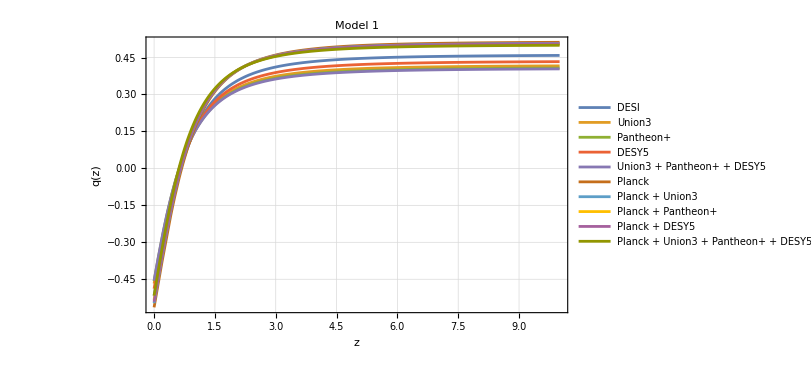

```mathematica
Plot[Evaluate[Table[qSolAllSets1[d][z],{d,Keys[qSolAllSets1]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[qSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.55,0.25}],Frame->True,FrameLabel->{"z","q(z)"},PlotLabel->"Model 1",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

#### Model 2, All datasets

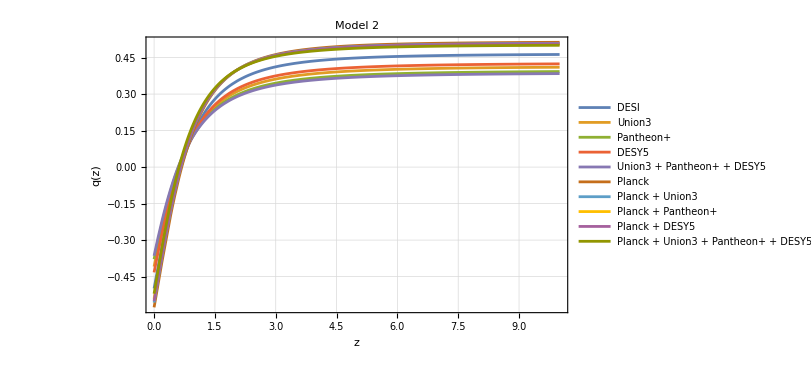

```mathematica
Plot[Evaluate[Table[qSolAllSets2[d][z],{d,Keys[qSolAllSets2]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[qSolAllSets2],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.55,0.25}],Frame->True,FrameLabel->{"z","q(z)"},PlotLabel->"Model 2",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

#### Model 3, All datasets

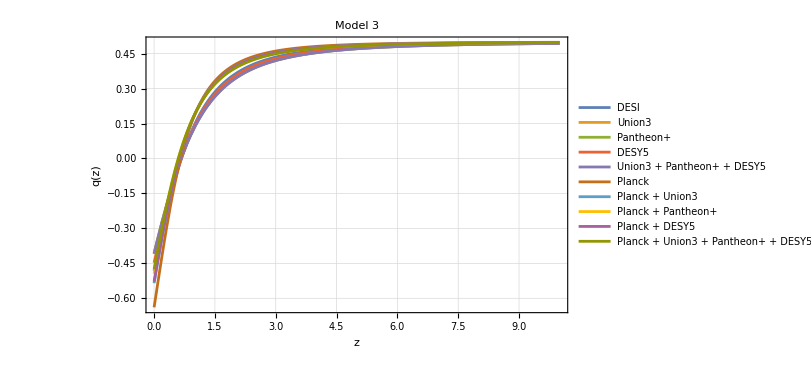

```mathematica
Plot[Evaluate[Table[qSolAllSets3[d][z],{d,Keys[qSolAllSets3]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[qSolAllSets3],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.55,0.25}],Frame->True,FrameLabel->{"z","q(z)"},PlotRange->All,PlotLabel->"Model 3",GridLines->Automatic,ImageSize->600]
```

#### Plotting for a specific dataset

```mathematica
AvailableDatasets["Model 1"]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
DataSetPlot=AvailableDatasets["Model 1"][[1]]
```

DESI

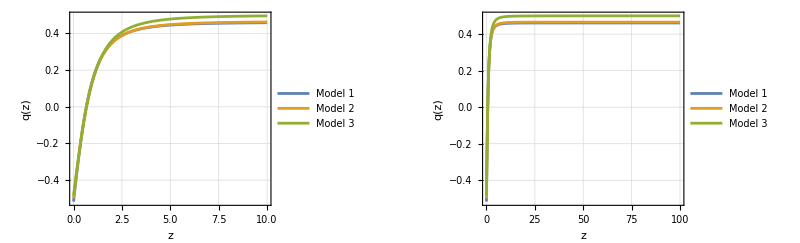

```mathematica
GraphicsRow[{
Plot[{qSolAllSets1[DataSetPlot][z],qSolAllSets2[DataSetPlot][z],qSolAllSets3[DataSetPlot][z]},{z,0,zPlot},FrameLabel->{"z","q(z)"},GridLines->Automatic,ImageSize->Full,Frame->True,PlotRange->All,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]],
Plot[{qSolAllSets1[DataSetPlot][z],qSolAllSets2[DataSetPlot][z],qSolAllSets3[DataSetPlot][z]},{z,0,zinitial},FrameLabel->{"z","q(z)"},GridLines->Automatic,Frame->True,PlotRange->All,ImageSize->Full,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]]},ImageSize->Full]
```

### Obtaining E(z)

```mathematica
SolveForEh[model_String,dataset_String]:=
Module[{params,qFn,odeEh,sol},
params=GetParams[model,dataset];
qFn=SolveForq[model,dataset];

odeEh={(dEh/. q->qFn)/. ϵ->params["eps"],Eh[0]==1};
sol=NDSolve[odeEh,Eh,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10];
Eh/. sol[[1]]];
```

```mathematica
ESolAllSets1=Association[Map[#->SolveForEh["Model 1",#]&,AvailableDatasets["Model 1"]]];
ESolAllSets2=Association[Map[#->SolveForEh["Model 2",#]&,AvailableDatasets["Model 2"]]];
ESolAllSets3=Association[Map[#->SolveForEh["Model 3",#]&,AvailableDatasets["Model 3"]]];
```

#### Model 1, All datasets

```mathematica
Plot[Evaluate[Table[hSolAllSets1[d][z],{d,Keys[hSolAllSets1]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[hSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.45,0.8}],Frame->True,FrameLabel->{"z","h(z)"},PlotLabel->"Model 1",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

Keys::invrl: The argument hSolAllSets1 is not a valid Association or a list of rules.

Table::iterb: Iterator {d,Keys[hSolAllSets1]} does not have appropriate bounds.

Keys::invrl: The argument hSolAllSets1 is not a valid Association or a list of rules.

Table::iterb: Iterator {d,Keys[hSolAllSets1]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics-

```mathematica
TableForm[Table[{d,hSolAllSets1[d][zinitial]},{d,Keys[hSolAllSets1]}],TableHeadings->{None,{"Dataset","h(zInitial)"}}]
```

Keys::invrl: The argument hSolAllSets1 is not a valid Association or a list of rules.

Table::iterb: Iterator {d,Keys[hSolAllSets1]} does not have appropriate bounds.

Table[{d,hSolAllSets1[d][zinitial]},{d,Keys[hSolAllSets1]}]

#### Model 2, All datasets

```mathematica
Plot[Evaluate[Table[hSolAllSets2[d][z],{d,Keys[hSolAllSets2]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[hSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.45,0.8}],Frame->True,FrameLabel->{"z","h(z)"},PlotLabel->"Model 2",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

Keys::invrl: The argument hSolAllSets2 is not a valid Association or a list of rules.

Table::iterb: Iterator {d,Keys[hSolAllSets2]} does not have appropriate bounds.

Keys::invrl: The argument hSolAllSets1 is not a valid Association or a list of rules.

Table::iterb: Iterator {d,Keys[hSolAllSets2]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics-

```mathematica
TableForm[Table[{d,hSolAllSets2[d][zinitial]},{d,Keys[hSolAllSets2]}],TableHeadings->{None,{"Dataset","h(zInitial)"}}]
```

Keys::invrl: The argument hSolAllSets2 is not a valid Association or a list of rules.

Table::iterb: Iterator {d,Keys[hSolAllSets2]} does not have appropriate bounds.

Table[{d,hSolAllSets2[d][zinitial]},{d,Keys[hSolAllSets2]}]

#### Model 3, All datasets

```mathematica
Plot[Evaluate[Table[hSolAllSets3[d][z],{d,Keys[hSolAllSets3]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[hSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.45,0.8}],Frame->True,FrameLabel->{"z","h(z)"},PlotLabel->"Model 3",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

Keys::invrl: The argument hSolAllSets3 is not a valid Association or a list of rules.

Table::iterb: Iterator {d,Keys[hSolAllSets3]} does not have appropriate bounds.

Keys::invrl: The argument hSolAllSets1 is not a valid Association or a list of rules.

Table::iterb: Iterator {d,Keys[hSolAllSets3]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics-

```mathematica
TableForm[Table[{d,hSolAllSets3[d][zinitial]},{d,Keys[hSolAllSets3]}],TableHeadings->{None,{"Dataset","h(zInitial)"}}]
```

Keys::invrl: The argument hSolAllSets3 is not a valid Association or a list of rules.

Table::iterb: Iterator {d,Keys[hSolAllSets3]} does not have appropriate bounds.

Table[{d,hSolAllSets3[d][zinitial]},{d,Keys[hSolAllSets3]}]

#### Plotting for a specific dataset

```mathematica
AvailableDatasets["Model 1"]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
DataSetPlot=AvailableDatasets["Model 1"][[1]]
```

DESI

```mathematica
GraphicsRow[{
Plot[{hSolAllSets1[DataSetPlot][z],hSolAllSets2[DataSetPlot][z],hSolAllSets3[DataSetPlot][z]},{z,0,zPlot},FrameLabel->{"z","h(z)"},GridLines->Automatic,ImageSize->Full,Frame->True,PlotRange->All,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]],
Plot[{hSolAllSets1[DataSetPlot][z],hSolAllSets2[DataSetPlot][z],hSolAllSets3[DataSetPlot][z]},{z,0,zinitial},FrameLabel->{"z","h(z)"},GridLines->Automatic,Frame->True,PlotRange->All,ImageSize->Full,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]]},ImageSize->Full]
```

-Graphics-

### Matter density (Ω_m) Analysis

#### Modules

```mathematica
(*Compute Ω_m(z) as an interpolating function for a given model/dataset*)SolveForOmegaM[model_String,dataset_String,EhSol_]:=
Module[{params,Om0},
params=GetParams[model,dataset];
Om0=params["Om0"];
Function[zval,Om0*(1+zval)^3/EhSol[zval]^2]];
```

```mathematica
PlotOmegaM[model_String,OmegaMAllSetsModel_Association,zmax_:zPlot]:=Module[{datasets,colours,legend},datasets=Keys[OmegaMAllSetsModel];
colours=ColorData[97,"ColorList"][[1;;Length[datasets]]];
legend=LineLegend[colours,datasets,LegendMarkerSize->20,LegendFunction->(Framed[#,RoundingRadius->0,Background->White,FrameStyle->Gray]&)];
Plot[Evaluate[Table[OmegaMAllSetsModel[ds][z],{ds,datasets}]],{z,0,zmax},PlotStyle->colours,PlotLegends->Placed[legend,Right],PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"z","Ω_m(z)"},PlotLabel->model,ImageSize->600]];
```

#### Model 1

```mathematica
OmegaMAllSets1=Association[Map[#->SolveForOmegaM["Model 1",#,ESolAllSets1[#]]&,AvailableDatasets["Model 1"]]];
```

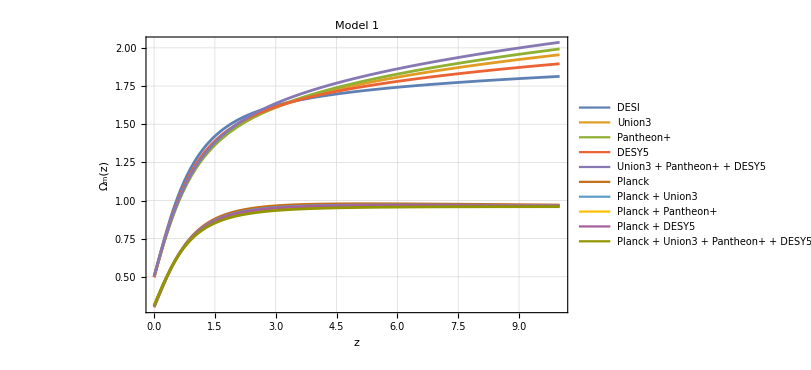

```mathematica
PlotOmegaM["Model 1",OmegaMAllSets1]
```

#### Model 2

```mathematica
OmegaMAllSets2=Association[Map[#->SolveForOmegaM["Model 2",#,ESolAllSets2[#]]&,AvailableDatasets["Model 2"]]];
```

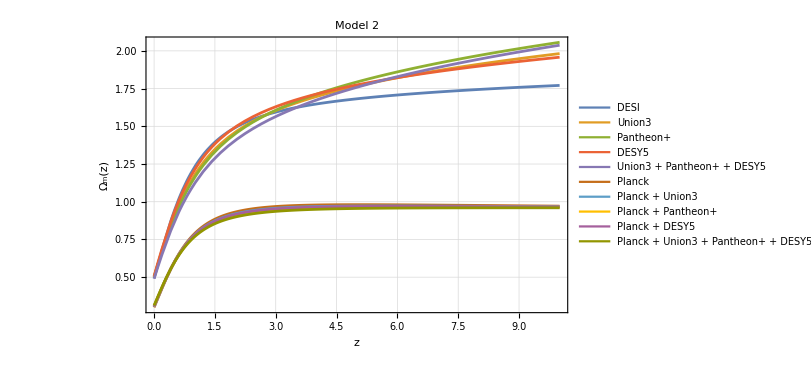

```mathematica
PlotOmegaM["Model 2",OmegaMAllSets2]
```

#### Model 3

```mathematica
OmegaMAllSets3=Association[Map[#->SolveForOmegaM["Model 3",#,ESolAllSets3[#]]&,AvailableDatasets["Model 3"]]];
```

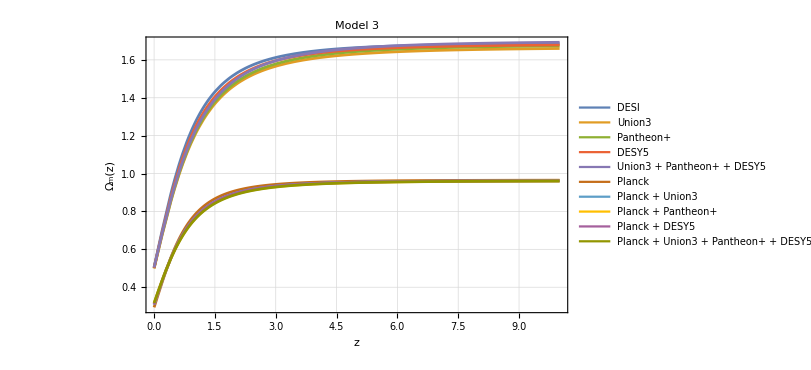

```mathematica
PlotOmegaM["Model 3",OmegaMAllSets3]
```

### DE equation of state

#### Modules

```mathematica
SolveForwDE[model_String,dataset_String,qSol_,OmegaMSol_]:=Module[{},Function[zval,(2*qSol[zval]-1)/(3*(1-OmegaMSol[zval]))]];
```

```mathematica
PlotwDE[model_String,wDEAllSetsModel_Association,datasets_List]:=Module[{colors,plotwDE},colors=ColorData[97,"ColorList"][[1;;Length[datasets]]];
plotwDE=Plot[Evaluate[Table[wDEAllSetsModel[d][z],{d,datasets}]],{z,0,zPlot},PlotStyle->colors,PlotLegends->Placed[LineLegend[colors,datasets,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}],Frame->True,FrameLabel->{"z","w_DE(z)"},PlotLabel->model<>" – w_DEz)",GridLines->Automatic,PlotRange->Automatic,ImageSize->800];
plotwDE];
```

#### Model 1

```mathematica
wDEAllSets1=Association[Map[#->SolveForwDE["Model 1",#,qSolAllSets1[#],OmegaMAllSets1[#]]&,AvailableDatasets["Model 1"]]];
```

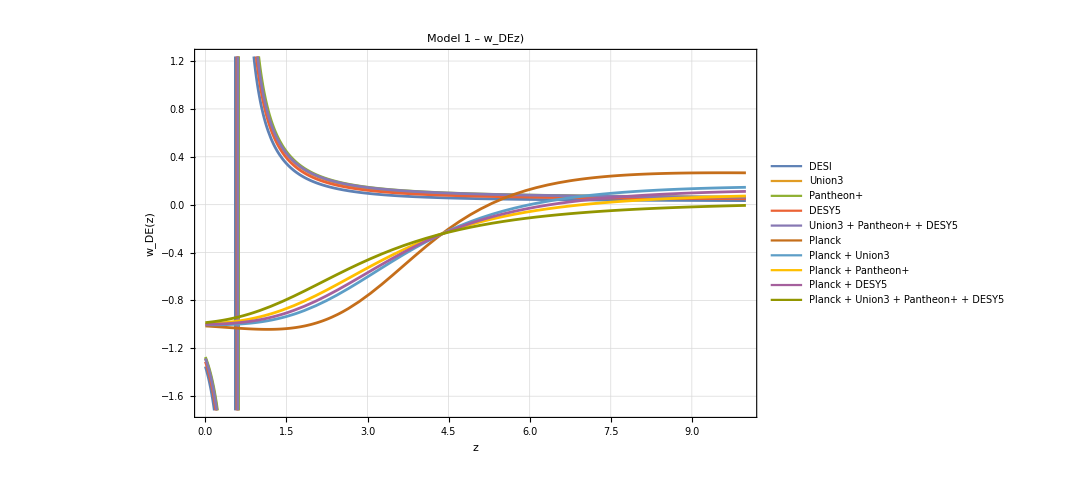

```mathematica
plotwDE1=PlotwDE["Model 1",wDEAllSets1,AvailableDatasets["Model 1"]];
plotwDE1
```

#### Model 2

```mathematica
wDEAllSets2=Association[Map[#->SolveForwDE["Model 2",#,qSolAllSets2[#],OmegaMAllSets2[#]]&,AvailableDatasets["Model 2"]]];
```

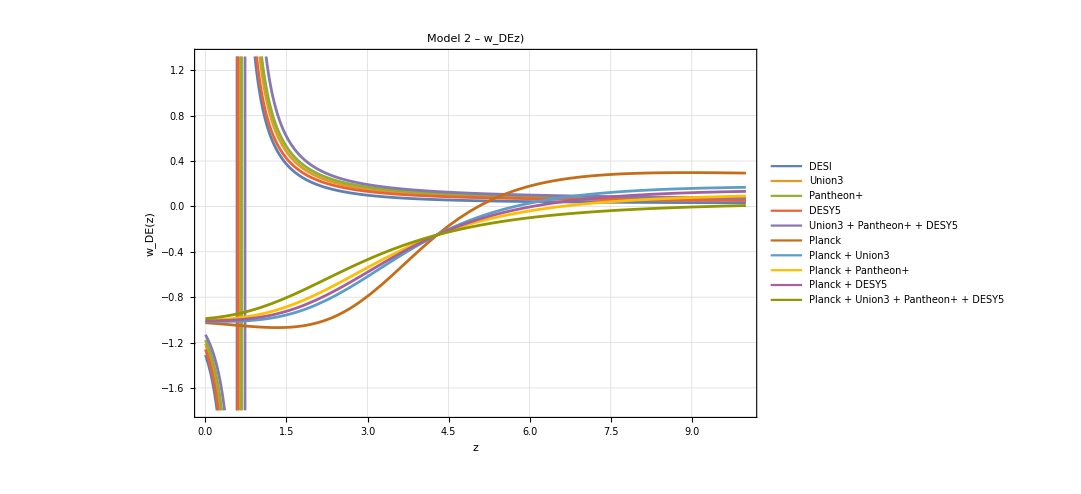

```mathematica
plotwDE2=PlotwDE["Model 2",wDEAllSets2,AvailableDatasets["Model 2"]]
```

#### Model 3:

```mathematica
wDEAllSets3=Association[Map[#->SolveForwDE["Model 3",#,qSolAllSets3[#],OmegaMAllSets3[#]]&,AvailableDatasets["Model 3"]]];
```

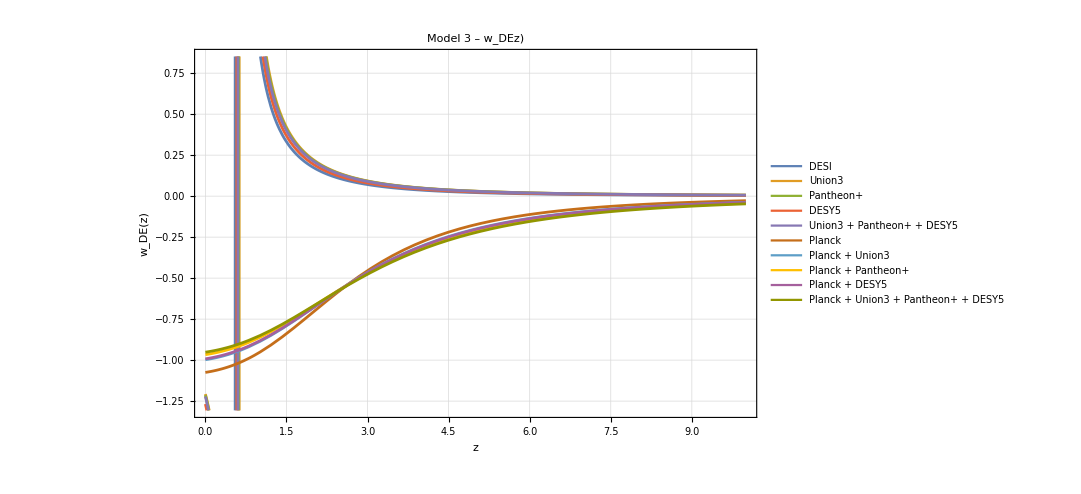

```mathematica
plotwDE3=PlotwDE["Model 3",wDEAllSets3,AvailableDatasets["Model 3"]]
```

## Determining suitable initial conditions for x_in and Ω_in:

### Modules

#### Classification of eigenvectors:

```mathematica
ClassifyEigenvectors[fp_Association]:=
Module[{eig,vecs,unstableIdx,stableIdx,vq,vxOmega,qComponents},

eig=fp["eigenvalues"];
vecs=fp["eigenvectors"];

unstableIdx=Flatten[Position[eig,_?(Re[#]>0&)]];
stableIdx=Flatten[Position[eig,_?(Re[#]<0&)]];

(*Among the unstable ones,find which has nonzero q-component*)
qComponents=vecs[[unstableIdx,3]];
vq=vecs[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]>10^-8&)]]]]]]];
vxOmega=vecs[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]<=10^-8&)]]]]]]];

<|"vq"->vq,"vxOmega"->vxOmega,"vStable"->vecs[[First[stableIdx]]],"lambdaQ"->eig[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]>10^-8&)]]]]]]],"lambdaXOmega"->eig[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]<=10^-8&)]]]]]]]|>];
```

#### Scan of ICs (Coarse)

```mathematica
ScanICs[model_String,dataset_String,c2Range_List]:=
Module[{fp,classified,vq,vxOmega,lambdaQ,qFn,deltaQ,c3,params,results},

fp=matterDominatedFPs[model][dataset];
classified=ClassifyEigenvectors[fp];
vq=classified["vq"];
vxOmega=classified["vxOmega"];
lambdaQ=classified["lambdaQ"];
params=GetParams[model,dataset];
qFn=SolveForq[model,dataset];
deltaQ=qFn[zinitial]-fp["q"];
c3=deltaQ/vq[[3]];

results=Table[Module[{x0,Ω0,sol,xFn,ΩFn,domainEnd,xFinal,ΩFinal},x0=fp["x"]+c2 vxOmega[[1]]+c3 vq[[1]];
Ω0=fp["Ω"]+c2 vxOmega[[2]]+c3 vq[[2]];
Block[{q,j,s,l,ϵ},
q[zz_]:=qFn[zz];
ϵ=params["eps"];
j[zz_]:=params["j"][zz];
s[zz_]:=Solve[dj,s[zz]][[1,1,2]];
l[zz_]:=Solve[ds,l[zz]][[1,1,2]]//Simplify;
sol=Quiet[Check[NDSolve[{dx,dΩ,x[zinitial]==x0,Ω[zinitial]==Ω0},{x,Ω},{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10],$Failed],NDSolve::ndsz];];
If[sol===$Failed,{c2,x0,Ω0,Indeterminate,Indeterminate,"Failed"},(xFn=x/. sol[[1]];
ΩFn=Ω/. sol[[1]];
domainEnd=xFn["Domain"][[1,1]];
If[domainEnd>0,{c2,x0,Ω0,Indeterminate,Indeterminate,"Diverged at z="<>ToString[domainEnd]},(xFinal=xFn[0];
ΩFinal=ΩFn[0];
{c2,x0,Ω0,xFinal,ΩFinal,If[xFinal<0&&ΩFinal>0,"Physical","Unphysical sign"]})])]],{c2,c2Range}];
results];
```

```mathematica
ScanAllDatasetsPhysical[model_String,c2Range_List]:=Module[{datasets,allResults,fullResultsByDataset,physicalRowsByDataset,bounds,sortedC2Range},datasets=AvailableDatasets[model];
sortedC2Range=Sort[c2Range];
fullResultsByDataset=Association[Map[Function[dataset,dataset->ScanICs[model,dataset,sortedC2Range]],datasets]];
physicalRowsByDataset=Association[Map[Function[dataset,dataset->Select[fullResultsByDataset[dataset],#[[-1]]==="Physical"&]],datasets]];
bounds=Association[Map[Function[dataset,Module[{fullRows,rows,c2Vals,minRow,maxRow,c2min,c2max,idxMin,idxMax,hasLowerBound,hasUpperBound},fullRows=fullResultsByDataset[dataset];
rows=physicalRowsByDataset[dataset];
If[Length[rows]==0,dataset-><|"c2min"->None,"c2max"->None,"xInAtMin"->None,"OmegaInAtMin"->None,"xInAtMax"->None,"OmegaInAtMax"->None,"count"->0,"hasLowerBound"->False,"hasUpperBound"->False|>,(c2Vals=rows[[All,1]];
c2min=Min[c2Vals];
c2max=Max[c2Vals];
minRow=First[Select[rows,#[[1]]==c2min&]];
maxRow=First[Select[rows,#[[1]]==c2max&]];
(*Index of c2min,c2max within the FULL sorted scan range*)idxMin=First[Flatten[Position[sortedC2Range,c2min]]];
idxMax=First[Flatten[Position[sortedC2Range,c2max]]];
(*Lower bound is confirmed if c2min isn't the first tested value,AND the point just below it is non-Physical*)hasLowerBound=(idxMin>1)&&(fullRows[[idxMin-1]][[-1]]=!="Physical");
(*Upper bound is confirmed if c2max isn't the last tested value,AND the point just above it is non-Physical*)hasUpperBound=(idxMax<Length[sortedC2Range])&&(fullRows[[idxMax+1]][[-1]]=!="Physical");
If[!hasLowerBound,Print[model," ",dataset," does not have a confirmed lower bound – widen the range downward."]];
If[!hasUpperBound,Print[model," ",dataset," does not have a confirmed upper bound – widen the range upward."]];
dataset-><|"c2min"->c2min,"c2max"->c2max,"xInAtMin"->minRow[[2]],"OmegaInAtMin"->minRow[[3]],"xInAtMax"->maxRow[[2]],"OmegaInAtMax"->maxRow[[3]],"count"->Length[rows],"hasLowerBound"->hasLowerBound,"hasUpperBound"->hasUpperBound|>)]]],datasets]];
allResults=Flatten[Map[Function[dataset,Map[Prepend[#,dataset]&,physicalRowsByDataset[dataset]]],datasets],1];
<|"table"->allResults,"byDataset"->physicalRowsByDataset,"bounds"->bounds|>];
```

#### Refine Scan and plot:

```mathematica
RefineScan[model_String,dataset_String,scanResults_Association,nPoints_Integer:50]:=
Module[{bnds,refinedRange},
bnds=scanResults["bounds"][dataset];
If[bnds["c2min"]===None,Return[$Failed]];
refinedRange=Subdivide[bnds["c2min"],bnds["c2max"],nPoints-1];
ScanICs[model,dataset,refinedRange]];
```

```mathematica
PlotRefinedScan[model_String,dataset_String,refinedResults_List]:=
Module[{physicalRows,sorted,xInVals,x0Vals,Omega0Vals},
physicalRows=Select[refinedResults,#[[-1]]==="Physical"&];
If[Length[physicalRows]==0,Print["No physical points found for ",dataset," in this range."];
Return[$Failed]];
sorted=SortBy[physicalRows,#[[2]]&];(*sort by x_in*)xInVals=sorted[[All,2]];
x0Vals=sorted[[All,4]];
Omega0Vals=sorted[[All,5]];
ListLinePlot[{Transpose[{xInVals,x0Vals}],Transpose[{xInVals,Omega0Vals}]},PlotLegends->Placed[LineLegend[{"x(0)","Ω(0)"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}],Frame->True,FrameLabel->{"x_in","value"},PlotLabel->model<>", "<>dataset,GridLines->Automatic,ImageSize->600,PlotMarkers->{Automatic, Small}]];
```

#### Determining ICs to be used within range

```mathematica
FindCalibratedIC[model_String,dataset_String,scanResults_Association,tolerance_:0.05]:=
Module[{bnds,om0Target,refined,physicalRows,negXRows,withinTol,closest},
bnds=scanResults["bounds"][dataset];
If[bnds["c2min"]===None,Return[$Failed]];
om0Target=GetParams[model,dataset]["Om0"];
refined=RefineScan[model,dataset,scanResults,200];
physicalRows=Select[refined,#[[-1]]==="Physical"&];
If[Length[physicalRows]==0,Return[$Failed]];

(*Require x_in<0 (genuine GR-viable sign),not just x(0)<0*)
negXRows=Select[physicalRows,#[[2]]<0&];
If[Length[negXRows]==0,Print[dataset,": no physical point has x_in < 0 (all x_in ≥ 0 for this dataset/model) – returning None."];
Return[None]];

(*Among x_in<0 points,find those within tolerance of Om0_mean*)withinTol=Select[negXRows,Abs[#[[5]]-om0Target]/om0Target<tolerance&];
If[Length[withinTol]>0,closest=First[withinTol];
<|"c2"->closest[[1]],"xIn"->closest[[2]],"OmegaIn"->closest[[3]],"x0"->closest[[4]],"Omega0"->closest[[5]],"Om0Target"->om0Target,"relativeDiff"->Abs[closest[[5]]-om0Target]/om0Target|>,(closest=First[SortBy[negXRows,Abs[#[[5]]-om0Target]&]];
Print[dataset,": no x_in<0 point within ",Round[100 tolerance],"% of Om0=",om0Target,"; closest available has Ω0=",closest[[5]]];
<|"c2"->closest[[1]],"xIn"->closest[[2]],"OmegaIn"->closest[[3]],"x0"->closest[[4]],"Omega0"->closest[[5]],"Om0Target"->om0Target,"relativeDiff"->Abs[closest[[5]]-om0Target]/om0Target|>)]];
```

### Model 1

#### Initial scan (coarse)

```mathematica
c2TestRange=Join[-Reverse[10^Range[-8,-2,0.1]],10^Range[-8,-2,0.1]];
```

```mathematica
scanResultsModel1=ScanAllDatasetsPhysical["Model 1",c2TestRange];
```

```mathematica
Grid[Prepend[Table[{
dataset,
scanResultsModel1["bounds"][dataset]["c2min"],
scanResultsModel1["bounds"][dataset]["c2max"],
scanResultsModel1["bounds"][dataset]["xInAtMin"],
scanResultsModel1["bounds"][dataset]["xInAtMax"],
scanResultsModel1["bounds"][dataset]["OmegaInAtMin"],
scanResultsModel1["bounds"][dataset]["OmegaInAtMax"],
scanResultsModel1["bounds"][dataset]["count"]},{dataset,AvailableDatasets["Model 1"]}],{"Dataset","c_2(a)","c_2(b)","x_in(a)","x_in(b)","Ω_in(a)","Ω_in(b)","# physical"}],Frame->All]
```

Dataset | c_2(a) | c_2(b) | x_in(a) | x_in(b) | Ω_in(a) | Ω_in(b) | # physical
DESI | -5.01187×10^-7 | 2.51189×10^-7 | -0.0775185 | -0.0775178 | 0.908558 | 0.908558 | 33
Union3 | -1.×10^-7 | 5.01187×10^-7 | -0.1625 | -0.1625 | 0.806012 | 0.806012 | 29
Pantheon+ | -1.99526×10^-8 | 6.30957×10^-7 | -0.180312 | -0.180311 | 0.784215 | 0.784214 | 23
DESY5 | -2.51189×10^-7 | 3.98107×10^-7 | -0.128173 | -0.128172 | 0.847724 | 0.847724 | 32
Union3 + Pantheon+ + DESY5 | 1.99526×10^-8 | 6.30957×10^-7 | -0.187075 | -0.187074 | 0.77591 | 0.77591 | 16
Planck | -1.×10^-6 | -1.25893×10^-7 | 0.0288434 | 0.0288442 | 1.03351 | 1.03351 | 10
Planck + Union3 | -1.×10^-6 | -7.94328×10^-8 | 0.0196607 | 0.0196616 | 1.02287 | 1.02287 | 12
Planck + Pantheon+ | -1.×10^-6 | -5.01187×10^-8 | 0.0128653 | 0.0128662 | 1.01498 | 1.01498 | 14
Planck + DESY5 | -1.×10^-6 | -6.30957×10^-8 | 0.0165382 | 0.0165391 | 1.01925 | 1.01925 | 13
Planck + Union3 + Pantheon+ + DESY5 | -7.94328×10^-7 | -1.58489×10^-8 | 0.00396972 | 0.00397047 | 1.00463 | 1.00463 | 18

#### Refine Scan:

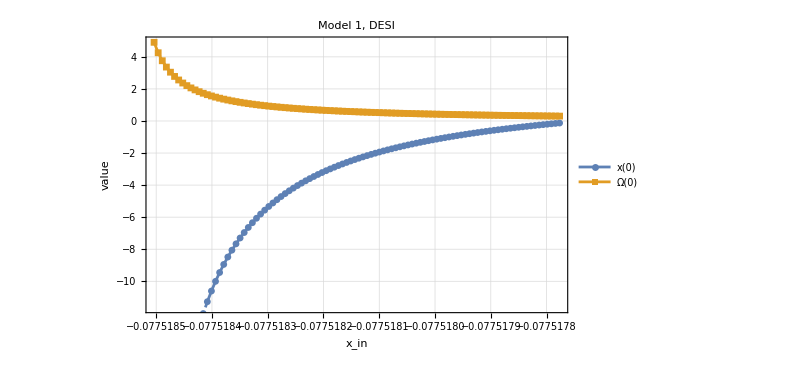

```mathematica
(*Plotting for 1 dataset*)
refinedDESI=RefineScan["Model 1","DESI",scanResultsModel1,100];
PlotRefinedScan["Model 1","DESI",refinedDESI]
```

```mathematica
allPlotsModel1=Table[Module[{refined},refined=RefineScan["Model 1",dataset,scanResultsModel1,100];
If[refined===$Failed,Print["Skipping ",dataset," – no physical region found (bounds were None)."];
Nothing,PlotRefinedScan["Model 1",dataset,refined]]],{dataset,AvailableDatasets["Model 1"]}];
```

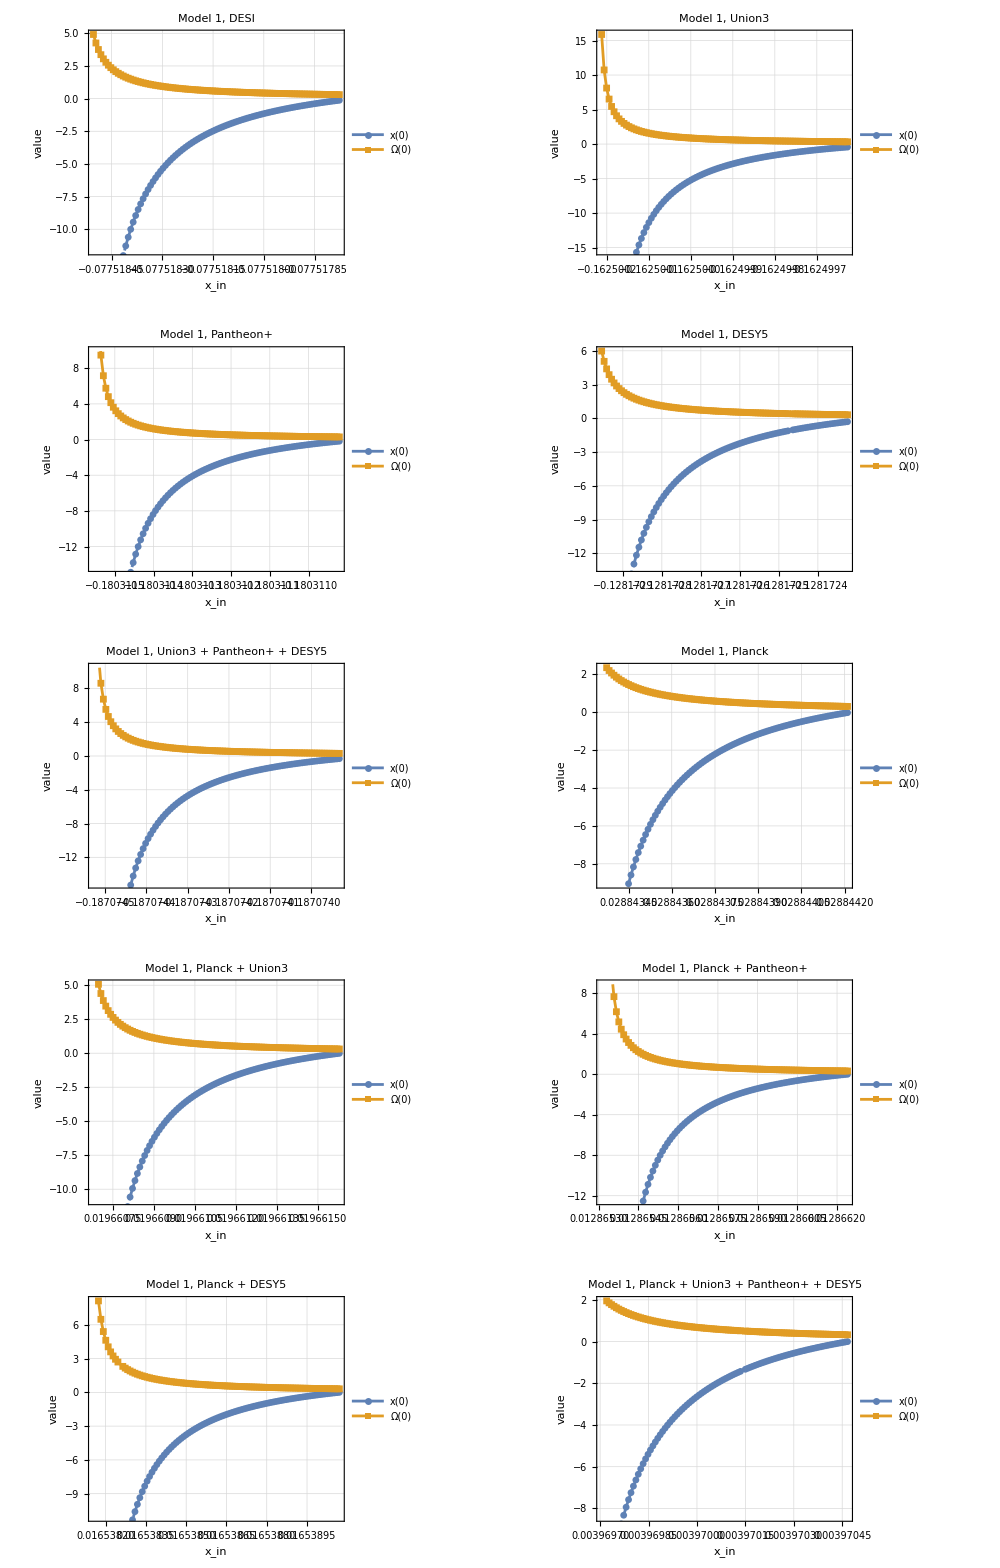

```mathematica
GraphicsGrid[Partition[allPlotsModel1,UpTo[2]],ImageSize->1000,Spacings->{20,20}]
```

#### Determining ICs to use

```mathematica
calibratedICsModel1=Association[Map[#->FindCalibratedIC["Model 1",#,scanResultsModel1,0.05]&,AvailableDatasets["Model 1"]]];;
```

Planck: no physical point has x_in < 0 (all x_in ≥ 0 for this dataset/model) – returning None.

Planck + Union3: no physical point has x_in < 0 (all x_in ≥ 0 for this dataset/model) – returning None.

Planck + Pantheon+: no physical point has x_in < 0 (all x_in ≥ 0 for this dataset/model) – returning None.

Planck + DESY5: no physical point has x_in < 0 (all x_in ≥ 0 for this dataset/model) – returning None.

Planck + Union3 + Pantheon+ + DESY5: no physical point has x_in < 0 (all x_in ≥ 0 for this dataset/model) – returning None.

```mathematica
(*Which datasets survive the x_in<0 requirement?*)viableDatasetsModel1=Select[AvailableDatasets["Model 1"],calibratedICsModel1[#]=!=None&];
excludedDatasetsModel1=Select[AvailableDatasets["Model 1"],calibratedICsModel1[#]===None&];
```

```mathematica
Print["Viable (x_in<0 found): ",viableDatasetsModel1];
Print["Excluded (no x_in<0 physical point): ",excludedDatasetsModel1];
```

Viable (x_in<0 found): {DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5}

Excluded (no x_in<0 physical point): {Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

### Model 2

#### Initial scan (coarse)

```mathematica
c2TestRange=Join[-Reverse[10^Range[-8,-2,0.1]],10^Range[-8,-2,0.1]];
```

```mathematica
scanResultsModel2=ScanAllDatasetsPhysical["Model 2",c2TestRange];
```

```mathematica
Grid[Prepend[Table[{
dataset,
scanResultsModel2["bounds"][dataset]["c2min"],
scanResultsModel2["bounds"][dataset]["c2max"],
scanResultsModel2["bounds"][dataset]["xInAtMin"],
scanResultsModel2["bounds"][dataset]["xInAtMax"],
scanResultsModel2["bounds"][dataset]["OmegaInAtMin"],
scanResultsModel2["bounds"][dataset]["OmegaInAtMax"],
scanResultsModel2["bounds"][dataset]["count"]},{dataset,AvailableDatasets["Model 1"]}],{"Dataset","c_2(a)","c_2(b)","x_in(a)","x_in(b)","Ω_in(a)","Ω_in(b)","# physical"}],Frame->All]
```

Dataset | c_2(a) | c_2(b) | x_in(a) | x_in(b) | Ω_in(a) | Ω_in(b) | # physical
DESI | -7.94328×10^-7 | 1.58489×10^-8 | -0.0683858 | -0.0683851 | 0.919435 | 0.919434 | 23
Union3 | -6.30957×10^-7 | 3.16228×10^-8 | -0.171988 | -0.171988 | 0.794411 | 0.794411 | 25
Pantheon+ | -5.01187×10^-7 | 3.16228×10^-8 | -0.207 | -0.206999 | 0.751351 | 0.751351 | 24
DESY5 | -6.30957×10^-7 | 3.16228×10^-8 | -0.144586 | -0.144585 | 0.827827 | 0.827827 | 25
Union3 + Pantheon+ + DESY5 | -5.01187×10^-7 | 3.16228×10^-8 | -0.223658 | -0.223658 | 0.73072 | 0.73072 | 24
Planck | -1.×10^-6 | -1.99526×10^-8 | 0.0304837 | 0.0304847 | 1.03541 | 1.03541 | 18
Planck + Union3 | -1.×10^-6 | -1.25893×10^-8 | 0.0214866 | 0.0214876 | 1.02499 | 1.02499 | 20
Planck + Pantheon+ | -7.94328×10^-7 | -1.×10^-8 | 0.0146281 | 0.0146289 | 1.01703 | 1.01703 | 20
Planck + DESY5 | -7.94328×10^-7 | -1.×10^-8 | 0.0184714 | 0.0184721 | 1.02149 | 1.02149 | 20
Planck + Union3 + Pantheon+ + DESY5 | -7.94328×10^-7 | -1.×10^-8 | 0.00556531 | 0.00556607 | 1.00649 | 1.00649 | 20

#### Refine Scan and plot:

```mathematica
allPlotsModel2=Table[
Module[{refined},
refined=RefineScan["Model 2",dataset,scanResultsModel2,100];
If[refined===$Failed,Print["Skipping ",dataset," – no physical region found (bounds were None)."];
Nothing,PlotRefinedScan["Model 2",dataset,refined]]],
{dataset,AvailableDatasets["Model 2"]}];
```

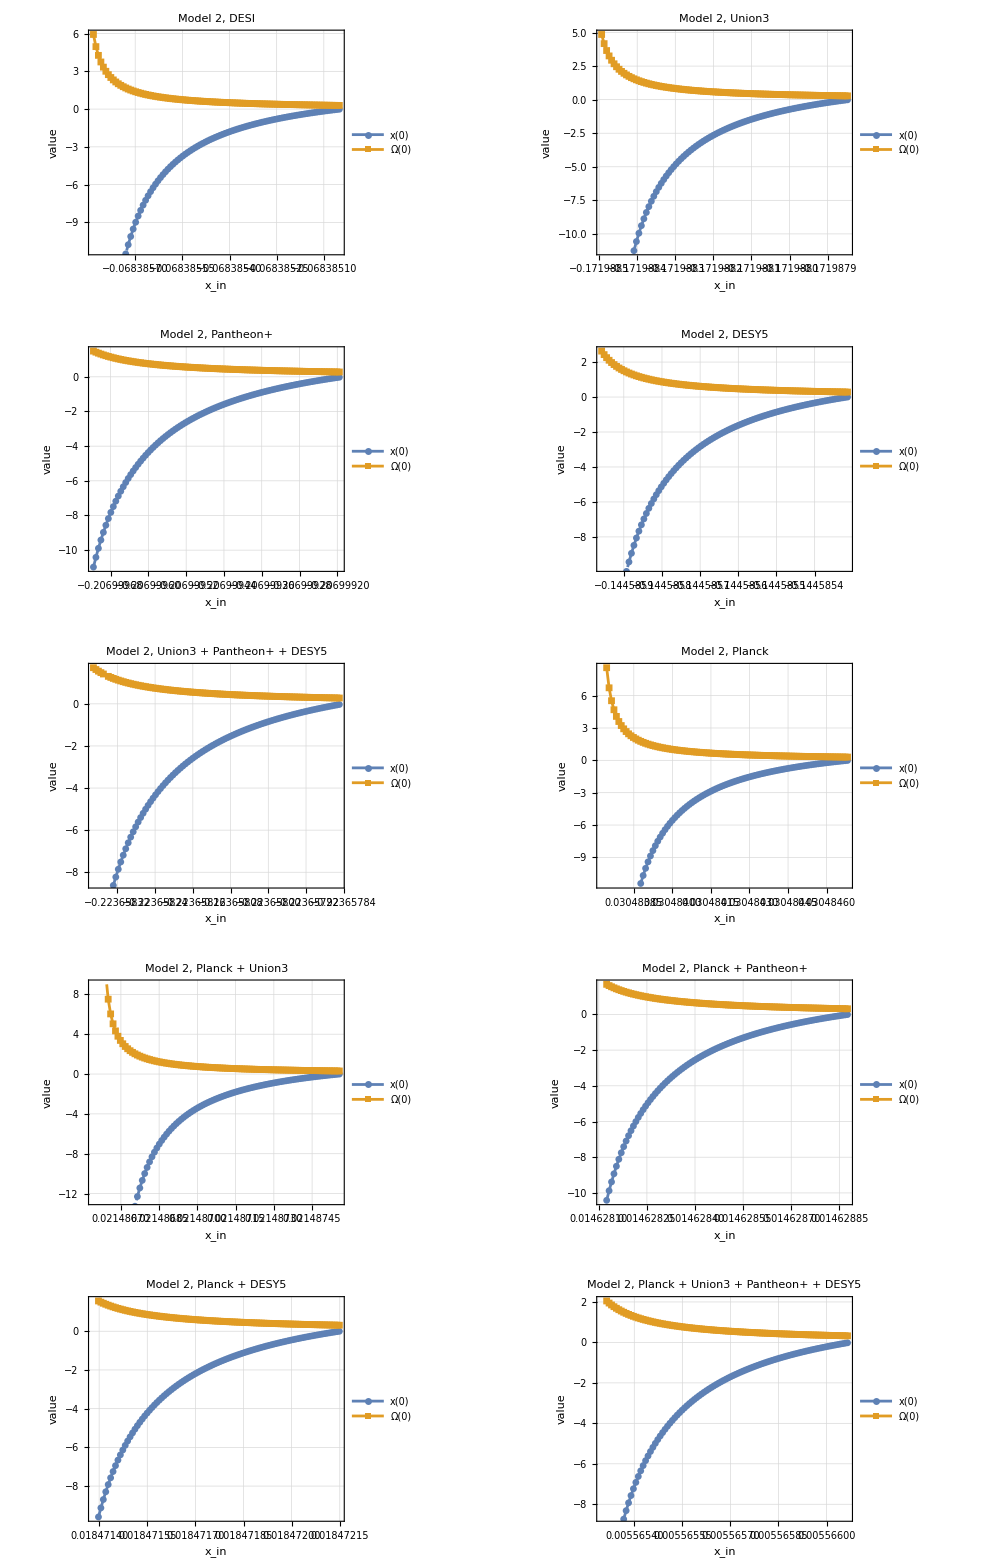

```mathematica
GraphicsGrid[Partition[allPlotsModel2,UpTo[2]],ImageSize->1000,Spacings->{20,20}]
```

#### Determining ICs to use

```mathematica
calibratedICsModel2=Association[Map[#->FindCalibratedIC["Model 2",#,scanResultsModel2,0.05]&,AvailableDatasets["Model 2"]]];;
```

Planck: no physical point has x_in < 0 (all x_in ≥ 0 for this dataset/model) – returning None.

Planck + Union3: no physical point has x_in < 0 (all x_in ≥ 0 for this dataset/model) – returning None.

Planck + Pantheon+: no physical point has x_in < 0 (all x_in ≥ 0 for this dataset/model) – returning None.

Planck + DESY5: no physical point has x_in < 0 (all x_in ≥ 0 for this dataset/model) – returning None.

Planck + Union3 + Pantheon+ + DESY5: no physical point has x_in < 0 (all x_in ≥ 0 for this dataset/model) – returning None.

```mathematica
(*Which datasets survive the x_in<0 requirement?*)viableDatasetsModel2=Select[AvailableDatasets["Model 2"],calibratedICsModel2[#]=!=None&];
excludedDatasetsModel2=Select[AvailableDatasets["Model 2"],calibratedICsModel2[#]===None&];
```

```mathematica
Print["Viable (x_in<0 found): ",viableDatasetsModel2];
Print["Excluded (no x_in<0 physical point): ",excludedDatasetsModel2];
```

Viable (x_in<0 found): {DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5}

Excluded (no x_in<0 physical point): {Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

### Model 3

#### Initial scan (coarse)

```mathematica
c2TestRange=Join[-Reverse[10^Range[-8,-3,0.05]],10^Range[-8,-3,0.05]];
```

```mathematica
scanResultsModel3=ScanAllDatasetsPhysical["Model 3",c2TestRange];
```

```mathematica
Grid[Prepend[Table[{
dataset,
scanResultsModel3["bounds"][dataset]["c2min"],
scanResultsModel3["bounds"][dataset]["c2max"],
scanResultsModel3["bounds"][dataset]["xInAtMin"],
scanResultsModel3["bounds"][dataset]["xInAtMax"],
scanResultsModel3["bounds"][dataset]["OmegaInAtMin"],
scanResultsModel3["bounds"][dataset]["OmegaInAtMax"],
scanResultsModel3["bounds"][dataset]["count"]},{dataset,AvailableDatasets["Model 3"]}],{"Dataset","c_2(a)","c_2(b)","x_in(a)","x_in(b)","Ω_in(a)","Ω_in(b)","# physical"}],Frame->All]
```

Dataset | c_2(a) | c_2(b) | x_in(a) | x_in(b) | Ω_in(a) | Ω_in(b) | # physical
DESI | -1.99526×10^-6 | -1.25893×10^-6 | -1.91355×10^-6 | -1.20737×10^-6 | 0.999995 | 0.999995 | 5
Union3 | -5.62341×10^-6 | -5.01187×10^-6 | -5.39313×10^-6 | -4.80663×10^-6 | 0.999989 | 0.999988 | 2
Pantheon+ | -5.62341×10^-6 | -5.01187×10^-6 | -5.39313×10^-6 | -4.80663×10^-6 | 0.999988 | 0.999988 | 2
DESY5 | -3.16228×10^-6 | -2.51189×10^-6 | -3.03278×10^-6 | -2.40902×10^-6 | 0.999993 | 0.999992 | 3
Union3 + Pantheon+ + DESY5 | -5.62341×10^-6 | -5.01187×10^-6 | -5.39313×10^-6 | -4.80663×10^-6 | 0.999988 | 0.999988 | 2
Planck | -5.01187×10^-7 | 4.46684×10^-7 | -4.80663×10^-7 | 4.28392×10^-7 | 0.999999 | 0.999999 | 69
Planck + Union3 | -7.94328×10^-7 | 1.12202×10^-7 | -7.618×10^-7 | 1.07607×10^-7 | 0.999999 | 0.999998 | 61
Planck + Pantheon+ | -1.×10^-6 | -1.77828×10^-7 | -9.59049×10^-7 | -1.70546×10^-7 | 0.999998 | 0.999998 | 16
Planck + DESY5 | -7.94328×10^-7 | 7.94328×10^-8 | -7.618×10^-7 | 7.618×10^-8 | 0.999998 | 0.999998 | 58
Planck + Union3 + Pantheon+ + DESY5 | -1.25893×10^-6 | -3.98107×10^-7 | -1.20737×10^-6 | -3.81804×10^-7 | 0.999997 | 0.999997 | 11

#### Refine Scan:

```mathematica
allPlotsModel3=Table[
Module[{refined},
refined=RefineScan["Model 3",dataset,scanResultsModel3,100];
If[refined===$Failed,Print["Skipping ",dataset," – no physical region found (bounds were None)."];
Nothing,PlotRefinedScan["Model 3",dataset,refined]]],
{dataset,AvailableDatasets["Model 3"]}];
```

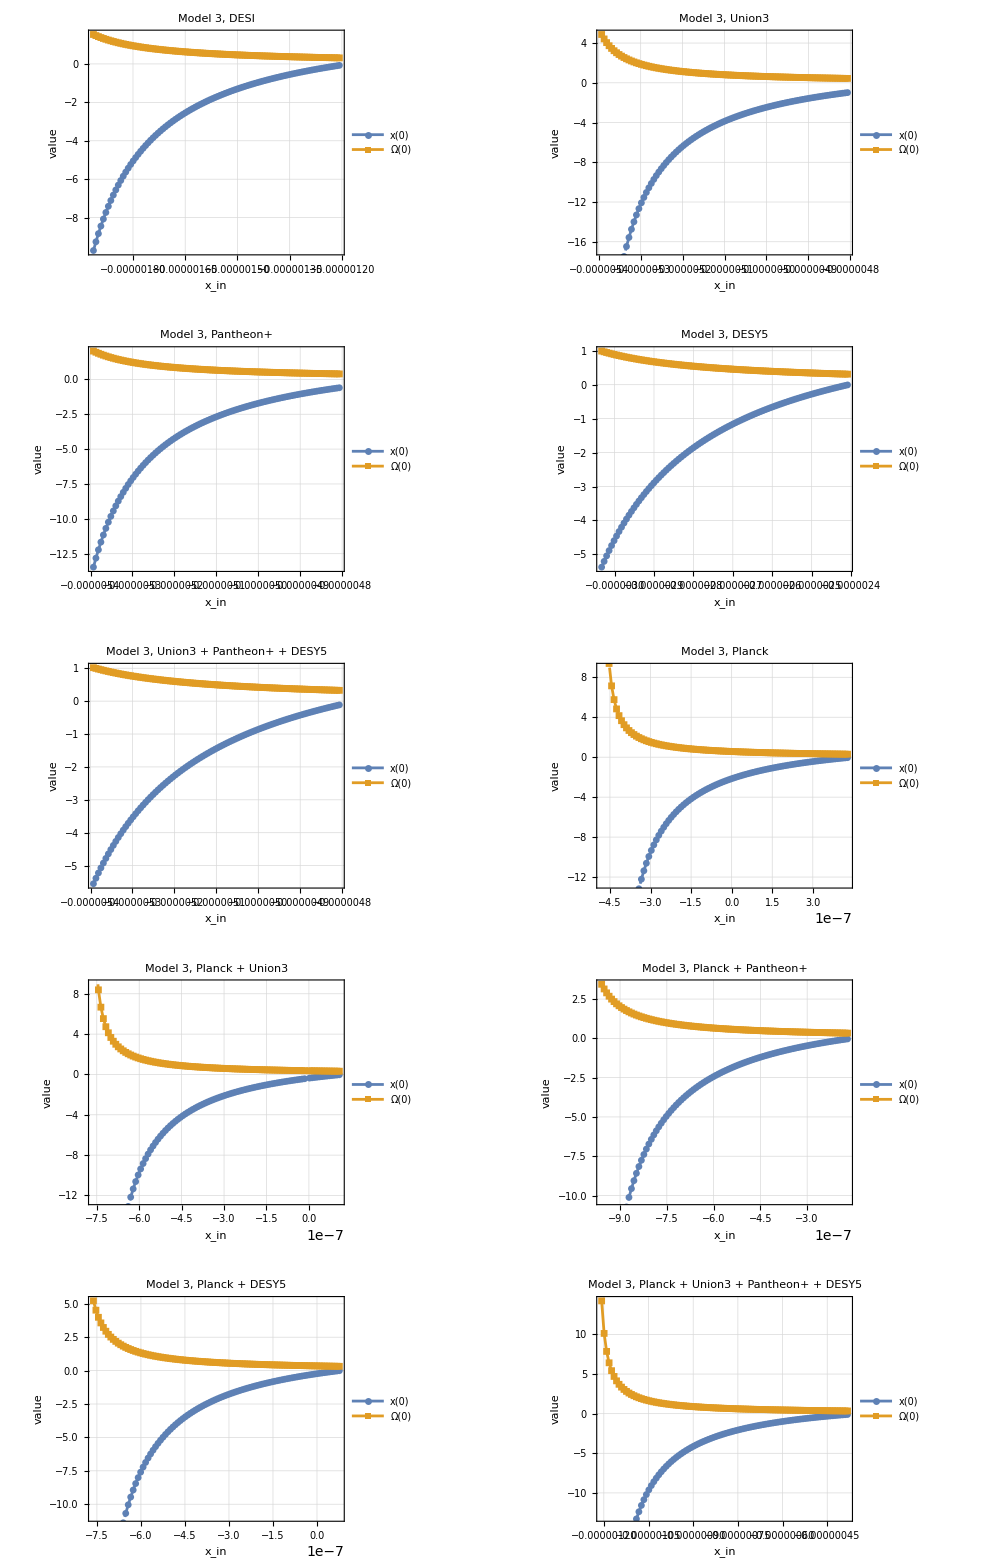

```mathematica
GraphicsGrid[Partition[allPlotsModel3,UpTo[2]],ImageSize->1000,Spacings->{20,20}]
```

#### Determining ICs to use

```mathematica
calibratedICsModel3=Association[Map[#->FindCalibratedIC["Model 3",#,scanResultsModel3,0.05]&,AvailableDatasets["Model 3"]]];;
```

Planck: no x_in<0 point within 5% of Om0=0.293759; closest available has Ω0=0.570112

Planck + Union3: no x_in<0 point within 5% of Om0=0.308245; closest available has Ω0=0.368114

Planck + Pantheon+: no x_in<0 point within 5% of Om0=0.313919; closest available has Ω0=0.332762

Planck + DESY5: no x_in<0 point within 5% of Om0=0.309164; closest available has Ω0=0.352619

Planck + Union3 + Pantheon+ + DESY5: no x_in<0 point within 5% of Om0=0.316572; closest available has Ω0=0.345746

```mathematica
(*Which datasets survive the x_in<0 requirement?*)viableDatasetsModel3=Select[AvailableDatasets["Model 3"],calibratedICsModel3[#]=!=None&];
excludedDatasetsModel3=Select[AvailableDatasets["Model 3"],calibratedICsModel3[#]===None&];
```

```mathematica
Print["Viable (x_in<0 found): ",viableDatasetsModel3];
Print["Excluded (no x_in<0 physical point): ",excludedDatasetsModel3];
```

Viable (x_in<0 found): {DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

Excluded (no x_in<0 physical point): {}

## Obtaining Background solutions x(z) and Ω(z)

#### Modules

```mathematica
SolveBackground[model_String,dataset_String,calibratedICs_Association]:=Module[{params,qFn,z0,ic,x0,Ω0,q0,sol,xFn,ΩFn,domainEnd},ic=calibratedICs[dataset];
If[ic===$Failed||ic===None,Return[$Failed]];
params=GetParams[model,dataset];
qFn=SolveForq[model,dataset];
z0=zinitial;
x0=ic["xIn"];
Ω0=ic["OmegaIn"];
q0=qFn[zinitial];
Block[{q,j,s,l,ϵ},q[z_]=qFn[z];
ϵ=params["eps"];
j[z_]=params["j"][z];
s[z_]=Solve[dj,s[z]][[1,1,2]];
l[z_]=Solve[ds,l[z]][[1,1,2]]//Simplify;
sol=Quiet[NDSolve[{dx,dΩ,x[z0]==x0,Ω[z0]==Ω0},{x,Ω},{z,0,z0},PrecisionGoal->10,AccuracyGoal->10],NDSolve::ndsz][[1]];
xFn=x/. sol;
ΩFn=Ω/. sol;];
domainEnd=xFn["Domain"][[1,1]];
If[domainEnd>0,Print[dataset," is stiff/diverges at z ≃ ",domainEnd]];
<|"x"->xFn,"Ω"->ΩFn,"q"->qFn,"z0"->z0,"zinitial"->zinitial,"failedAtZ"->If[domainEnd>0,domainEnd,None],"x0"->x0,"Ω0"->Ω0,"q0"->q0|>];
```

```mathematica
PlotBackgroundSolutions[model_String,bgResults_Association,datasets_List]:=
Module[{colors,plotX,plotOmega},
colors=ColorData[97,"ColorList"][[1;;Length[datasets]]];

plotX=Plot[Evaluate[Table[bgResults[d]["x"][z],{d,datasets}]],{z,0,zPlot},PlotStyle->colors,PlotLegends->Placed[LineLegend[colors,datasets,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.6,0.3}],Frame->True,FrameLabel->{"z","x(z)"},PlotLabel->model<>" – x(z)",GridLines->Automatic,PlotRange->All,ImageSize->650];
plotOmega=Plot[Evaluate[Table[bgResults[d]["Ω"][z],{d,datasets}]],{z,0,zPlot},PlotStyle->colors,PlotLegends->Placed[LineLegend[colors,datasets,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.6,0.3}],Frame->True,FrameLabel->{"z","Ω(z)"},PlotLabel->model<>" – Ω(z)",GridLines->Automatic,PlotRange->All,ImageSize->650];

{plotX,plotOmega}];
```

### Model 1, All datasets

```mathematica
viableDatasetsModel1
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5}

```mathematica
bgResultsModel1Calibrated=Association[Map[#->SolveBackground["Model 1",#,calibratedICsModel1]&,viableDatasetsModel1]];
```

```mathematica
Grid[Prepend[Table[{dataset,bgResultsModel1Calibrated[dataset]["x0"],bgResultsModel1Calibrated[dataset]["Ω0"],bgResultsModel1Calibrated[dataset]["x"][0],bgResultsModel1Calibrated[dataset]["Ω"][0],GetParams["Model 1",dataset]["Om0"],Abs[bgResultsModel1Calibrated[dataset]["Ω"][0]-GetParams["Model 1",dataset]["Om0"]]/GetParams["Model 1",dataset]["Om0"],bgResultsModel1Calibrated[dataset]["failedAtZ"]},{dataset,viableDatasetsModel1}],{"Dataset","x_in","Ω_in","x(0)","Ω(0)","Om0 (MCMC)","Rel. diff","Failed at z"}],Frame->All]
```

Dataset | x_in | Ω_in | x(0) | Ω(0) | Om0 (MCMC) | Rel. diff | Failed at z
DESI | -0.0775181 | 0.908558 | -1.95781 | 0.523174 | 0.498537 | 0.0494188 | None
Union3 | -0.1625 | 0.806012 | -2.1236 | 0.520274 | 0.497985 | 0.0447581 | None
Pantheon+ | -0.180311 | 0.784214 | -2.19342 | 0.521295 | 0.498378 | 0.0459827 | None
DESY5 | -0.128173 | 0.847724 | -2.0467 | 0.520795 | 0.497558 | 0.0467029 | None
Union3 + Pantheon+ + DESY5 | -0.187074 | 0.77591 | -2.28161 | 0.52712 | 0.504365 | 0.0451169 | None

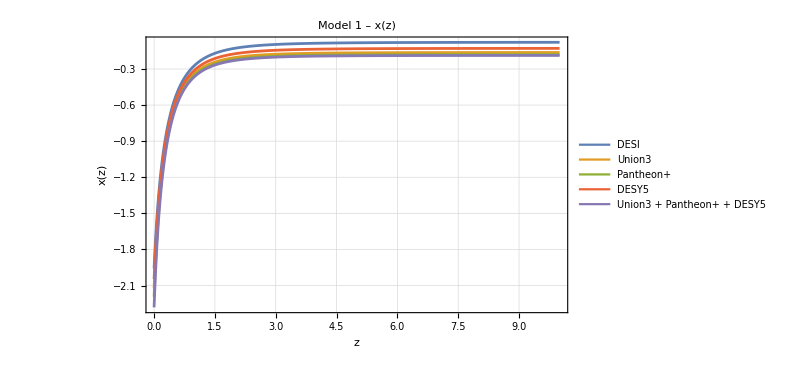

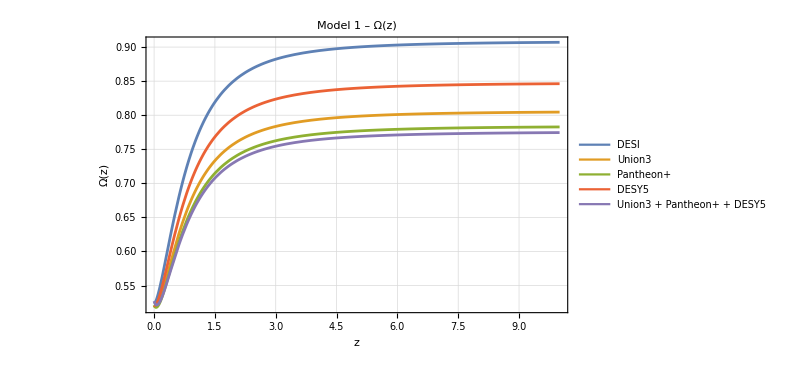

```mathematica
{plotXModel1,plotOmegaModel1}=PlotBackgroundSolutions["Model 1",bgResultsModel1Calibrated,viableDatasetsModel1];
plotXModel1
plotOmegaModel1
```

### Model 2, All datasets

```mathematica
viableDatasetsModel2
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5}

```mathematica
bgResultsModel2Calibrated=Association[Map[#->SolveBackground["Model 2",#,calibratedICsModel2]&,viableDatasetsModel2]];
```

```mathematica
Grid[Prepend[Table[{dataset,
bgResultsModel2Calibrated[dataset]["x0"],
bgResultsModel2Calibrated[dataset]["Ω0"],
bgResultsModel2Calibrated[dataset]["x"][0],
bgResultsModel2Calibrated[dataset]["Ω"][0],
GetParams["Model 2",dataset]["Om0"],
Abs[bgResultsModel2Calibrated[dataset]["Ω"][0]-GetParams["Model 2",dataset]["Om0"]]/GetParams["Model 2",dataset]["Om0"],bgResultsModel2Calibrated[dataset]["failedAtZ"]},{dataset,viableDatasetsModel2}],{"Dataset","x_in","Ω_in","x(0)","Ω(0)","Om0 (MCMC)","Rel. diff","Failed at z"}],Frame->All]
```

Dataset | x_in | Ω_in | x(0) | Ω(0) | Om0 (MCMC) | Rel. diff | Failed at z
DESI | -0.0683854 | 0.919435 | -1.83899 | 0.513468 | 0.491401 | 0.0449063 | None
Union3 | -0.171988 | 0.794411 | -2.13224 | 0.522494 | 0.500361 | 0.044234 | None
Pantheon+ | -0.206999 | 0.751351 | -2.26692 | 0.5258 | 0.503064 | 0.0451948 | None
DESY5 | -0.144586 | 0.827827 | -2.11673 | 0.528882 | 0.50687 | 0.0434287 | None
Union3 + Pantheon+ + DESY5 | -0.223658 | 0.73072 | -2.20055 | 0.511884 | 0.490353 | 0.0439082 | None

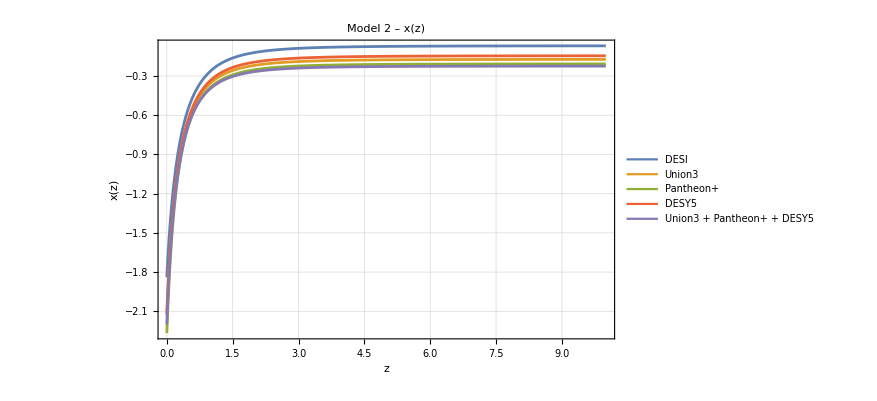

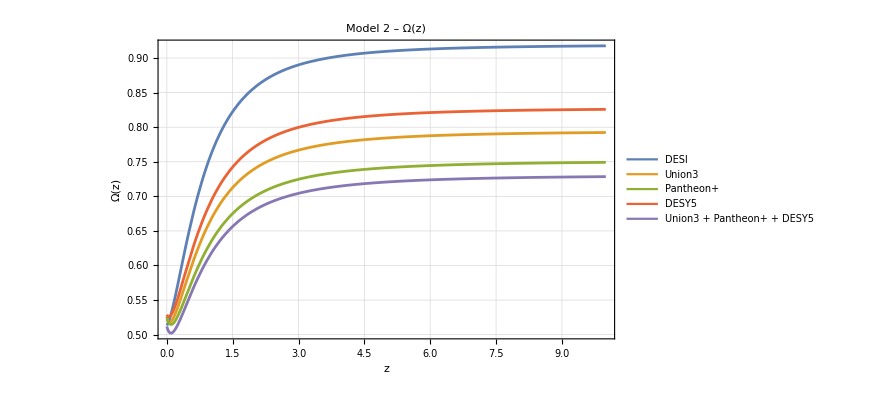

```mathematica
{plotXModel2,plotOmegaModel2}=PlotBackgroundSolutions["Model 2",bgResultsModel2Calibrated,viableDatasetsModel2];
plotXModel2
plotOmegaModel2
```

### Model 3, All datasets

```mathematica
viableDatasetsModel3
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
bgResultsModel3Calibrated=Association[Map[#->SolveBackground["Model 3",#,calibratedICsModel3]&,viableDatasetsModel3]];
```

```mathematica
Grid[Prepend[Table[{dataset,
bgResultsModel3Calibrated[dataset]["x0"],
bgResultsModel3Calibrated[dataset]["Ω0"],
bgResultsModel3Calibrated[dataset]["x"][0],
bgResultsModel3Calibrated[dataset]["Ω"][0],
GetParams["Model 3",dataset]["Om0"],
Abs[bgResultsModel3Calibrated[dataset]["Ω"][0]-GetParams["Model 3",dataset]["Om0"]]/GetParams["Model 3",dataset]["Om0"],bgResultsModel3Calibrated[dataset]["failedAtZ"]},{dataset,viableDatasetsModel3}],{"Dataset","x_in","Ω_in","x(0)","Ω(0)","Om0 (MCMC)","Rel. diff","Failed at z"}],Frame->All]
```

Dataset | x_in | Ω_in | x(0) | Ω(0) | Om0 (MCMC) | Rel. diff | Failed at z
DESI | -1.56579×10^-6 | 0.999995 | -1.76018 | 0.527853 | 0.503911 | 0.0475128 | None
Union3 | -4.90684×10^-6 | 0.999988 | -1.62318 | 0.522204 | 0.498632 | 0.0472734 | None
Pantheon+ | -4.99231×10^-6 | 0.999988 | -1.65651 | 0.525217 | 0.501271 | 0.0477691 | None
DESY5 | -2.78202×10^-6 | 0.999993 | -1.71304 | 0.526404 | 0.501897 | 0.0488273 | None
Union3 + Pantheon+ + DESY5 | -5.13377×10^-6 | 0.999988 | -1.68574 | 0.526745 | 0.504294 | 0.0445197 | None
Planck | -1.01121×10^-9 | 0.999999 | -2.16308 | 0.570112 | 0.293759 | 0.940743 | None
Planck + Union3 | -1.61489×10^-9 | 0.999998 | -0.374627 | 0.368114 | 0.308245 | 0.194227 | None
Planck + Pantheon+ | -1.70546×10^-7 | 0.999998 | -0.0365151 | 0.332762 | 0.313919 | 0.0600247 | None
Planck + DESY5 | -3.82814×10^-9 | 0.999998 | -0.245456 | 0.352619 | 0.309164 | 0.140556 | None
Planck + Union3 + Pantheon+ + DESY5 | -3.81804×10^-7 | 0.999997 | -0.0999386 | 0.345746 | 0.316572 | 0.0921571 | None

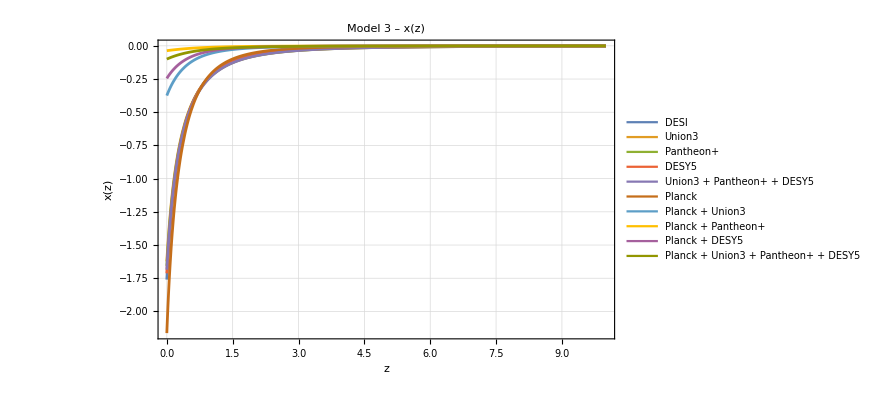
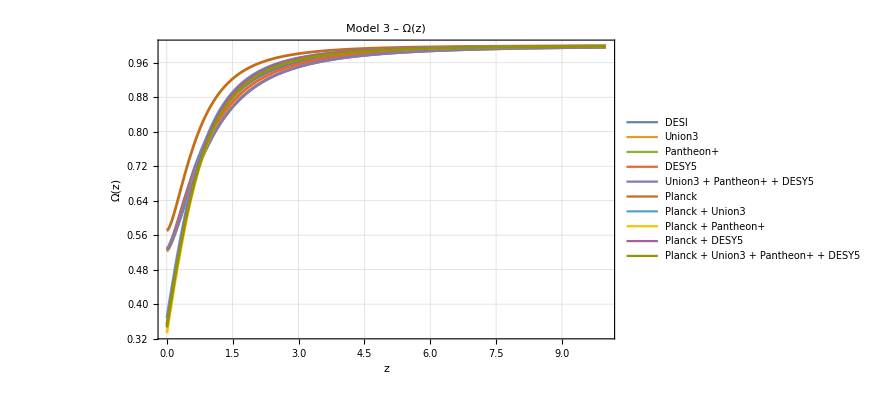

```mathematica
{plotXModel3,plotOmegaModel3}=PlotBackgroundSolutions["Model 3",bgResultsModel3Calibrated,viableDatasetsModel3];
{plotXModel3,plotOmegaModel3}
```

```mathematica
}
```